Material properties used by Eric:

```mathematica
ρ=0.008 10^6; cp=0.55 10^3; k=0.05 10^3; ω=0.2 10^-3; v=50 10^-3; Po=66.5;
```

```mathematica
η := k/(ρ cp); δ := 2 η/v; T0=20; Tm=880;
```

```mathematica
θ[P_,κ_,V_,x_,y_,z_]:= P/(2 π k √(x^2+y^2+z^2)(Tm-T0)) Exp[-V(√(x^2+y^2+z^2)+x)/(2 κ)];
```

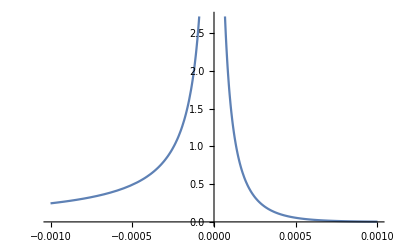

```mathematica
Plot[θ[Po,η,v,x,0,0],{x,-10 10^-4,10 10^-4}]
```

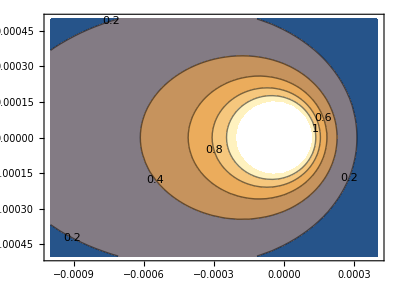

```mathematica
ContourPlot[θ[Po,η,v,x,y,0.0],{x,-10 10^-4,4 10^-4},{y,-5 10^-4,5 10^-4},ContourLabels->True, AspectRatio->True]
```

```mathematica
F[u_]:=1/(u π) Integrate[1-Exp[-2 u/(1+s^2)],{s,0,∞}]
υ[Po_,ω_,v_]:= Po/(k π ω) F[v ω/(2 η)]
```

```mathematica
υ[Po,ω,v]//N
```

1737.29